```mathematica
Pirates
```

```mathematica
Solve[{x(1+b(1-x))-r== 0,b>0,r>0,x>0},x,Reals]
```

{{x→ConditionalExpression[(1+b)/(2 b)-1/2 √((1+2 b+b^2-4 b r)/b^2),r>0&&2+1/b+b-4 r>0&&b>0]},{x→ConditionalExpression[(1+b)/(2 b)+1/2 √((1+2 b+b^2-4 b r)/b^2),r>0&&2+1/b+b-4 r>0&&b>0]}}

```mathematica
Demand for piracy Pirates
```

```mathematica
Simplify[1-((1+b)/(2 b)-1/2 √((1+2 b+b^2-4 b r)/b^2))]
```

(-1+b+b √((1+2 b+b^2-4 b r)/b^2))/(2 b)

```mathematica
Manipulate[Plot[(-1+b+b √((1+2 b+b^2-4 b r)/b^2))/(2 b),{r,0,8}],{b,0,8}]
```

```mathematica
Buyers
```

```mathematica
Simplify[Solve[{x*(1+a*((-1+b+b √((1+2 b+b^2-4 b r)/b^2))/(2 b))+k)-p== x*(1+b*((-1+b+b √((1+2 b+b^2-4 b r)/b^2))/(2 b)))-r,a≥ b>0,p>r>0,x>0},x,Reals]]
```

{{x→ConditionalExpression[(2 b (-p+r))/(-a (-1+b+√(1+2 b+b^2-4 b r))+b (-1+b-2 k+√(1+2 b+b^2-4 b r))),a>0&&p>r&&0<b<a&&((a/b+b<1+a+2 k&&r>0&&2+1/b+b>4 r)||(0<r<(a^2-2 a b+b^2+a k-b k-a b k+b^2 k-b k^2)/(a-b)^2&&a+k>b&&a/b+b>1+a+2 k))]}}

```mathematica
Buyer Demand
```

```mathematica
Simplify[1-((2 b (-p+r))/(-a (-1+b+√(1+2 b+b^2-4 b r))+b (-1+b-2 k+√(1+2 b+b^2-4 b r))))]
```

1+(2 b (p-r))/(-a (-1+b+√(1+2 b+b^2-4 b r))+b (-1+b-2 k+√(1+2 b+b^2-4 b r)))

```mathematica
Manipulate[Plot[{1+(2 b (p-r))/(-a (-1+b+√(1+2 b+b^2-4 b r))+b (-1+b-2 k+√(1+2 b+b^2-4 b r))),1},{p,1,10},PlotRange->{0,1}],{a,2,8},{b,0,2},{k,0,2},{r,0,1}]
```

```mathematica
Constraints
```

```mathematica
First constraint
```

```mathematica
1≥ 1+(2 b (p-r))/(-a (-1+b+√(1+2 b+b^2-4 b r))+b (-1+b-2 k+√(1+2 b+b^2-4 b r)))
```

```mathematica
p≥ r
```

```mathematica
Second Constraint
```

```mathematica
(-1+b+b √((1+2 b+b^2-4 b r)/b^2))/(2 b)≥ 1+(2 b (p-r))/(-a (-1+b+√(1+2 b+b^2-4 b r))+b (-1+b-2 k+√(1+2 b+b^2-4 b r)))
(-1-b+b √((1+2 b+b^2-4 b r)/b^2))(-a (-1+b+√(1+2 b+b^2-4 b r))+b (-1+b-2 k+√(1+2 b+b^2-4 b r)))≥ 2 b (p-r)*2 b
```

```mathematica
Concavity
```

```mathematica
D[D[p*(1-(2 b *(p-r))/(a* (-1+b+√(1+2 b+b^2-4 b r))-b* (-1+b-2 k+√(1+2 b+b^2-4 b r))))-k^2+H*(p-r)+T*((-1-b+b √((1+2 b+b^2-4 b r)/b^2))(-a (-1+b+√(1+2 b+b^2-4 b r))+b (-1+b-2 k+√(1+2 b+b^2-4 b r)))-4*b^2(p-r)),p],p]
```

-(4 b)/(a (-1+b+√(1+2 b+b^2-4 b r))-b (-1+b-2 k+√(1+2 b+b^2-4 b r)))

```mathematica
-(4 b)/((a-b) (-1+b+√(1+2 b+b^2-4 b r))+2*k*b)
```

```mathematica
Solve[{D[p*(1-(2 b *(p-r))/(a* (-1+b+√(1+2 b+b^2-4 b r))-b* (-1+b-2 k+√(1+2 b+b^2-4 b r))))-k^2+H*(p-r)+T*((-1-b+b √((1+2 b+b^2-4 b r)/b^2))(-a (-1+b+√(1+2 b+b^2-4 b r))+b (-1+b-2 k+√(1+2 b+b^2-4 b r)))-4*b^2(p-r)),k]==0,D[p*(1-(2 b *(p-r))/(a* (-1+b+√(1+2 b+b^2-4 b r))-b* (-1+b-2 k+√(1+2 b+b^2-4 b r))))-k^2+H*(p-r)+T*((-1-b+b √((1+2 b+b^2-4 b r)/b^2))(-a (-1+b+√(1+2 b+b^2-4 b r))+b (-1+b-2 k+√(1+2 b+b^2-4 b r)))-4*b^2(p-r)),p]==0,D[p*(1-(2 b *(p-r))/(a* (-1+b+√(1+2 b+b^2-4 b r))-b* (-1+b-2 k+√(1+2 b+b^2-4 b r))))-k^2+H*(p-r)+T*((-1-b+b √((1+2 b+b^2-4 b r)/b^2))(-a (-1+b+√(1+2 b+b^2-4 b r))+b (-1+b-2 k+√(1+2 b+b^2-4 b r)))-4*b^2(p-r)),H]==0,D[p*(1-(2 b *(p-r))/(a* (-1+b+√(1+2 b+b^2-4 b r))-b* (-1+b-2 k+√(1+2 b+b^2-4 b r))))-k^2+H*(p-r)+T*((-1-b+b √((1+2 b+b^2-4 b r)/b^2))(-a (-1+b+√(1+2 b+b^2-4 b r))+b (-1+b-2 k+√(1+2 b+b^2-4 b r)))-4*b^2(p-r)),T]==0,k>0,p>0,r>0,a>b>0,2+1/b+b-4 r>0,(a-b) (-1+b+√(1+2 b+b^2-4 b r))+2*k*b>0},{p,k,H,T},Reals]
```

$Aborted

```mathematica
Limit[p*(1-(2 b *(p-r))/(a* (-1+b+√(1+2 b+b^2-4 b r))-b* (-1+b-2 k+√(1+2 b+b^2-4 b r))))-k^2+H*(p-r)+T*((-1-b+b √((1+2 b+b^2-4 b r)/b^2))(-a (-1+b+√(1+2 b+b^2-4 b r))+b (-1+b-2 k+√(1+2 b+b^2-4 b r)))-4*b^2(p-r)),b-> 1]
```

```mathematica
D[-k^2+H (p-r)+p (1+(-p+r)/(k+(-1+a) √(1-r)))+4 (1+k-p-√(1-r)-k √(1-r)+a (-1+√(1-r)+r)) T,T]
```

4 (1+k-p-√(1-r)-k √(1-r)+a (-1+√(1-r)+r))

```mathematica
Solve[{1+H-p/(k+(-1+a) √(1-r))+(-p+r)/(k+(-1+a) √(1-r))-4 T==0,-2 k-(p (-p+r))/(k+(-1+a) √(1-r))^2+4 (1-√(1-r)) T==0,4 (1+k-p-√(1-r)-k √(1-r)+a (-1+√(1-r)+r))==0,k>0,p>0,1>r>0,a>1},{p,k,H,T},Reals]
```

```mathematica
Solve[{1+H-p/(k+(-1+a) √(1-r))+(-p+r)/(k+(-1+a) √(1-r))-4 T==0,-2 k-(p (-p+r))/(k+(-1+a) √(1-r))^2+4 (1-√(1-r)) T==0,4 (1+k-p-√(1-r)-k √(1-r)+a (-1+√(1-r)+r))==0,k>0,p>0,1>r>0,a>1},{p,k,T},Reals]
```

$Aborted

```mathematica
D[p*(1-(2 b *(p-r))/(a* (-1+b+√(1+2 b+b^2-4 b r))-b* (-1+b-2 k+√(1+2 b+b^2-4 b r))))-k^2+H*(p-r)+T*((-1-b+b √((1+2 b+b^2-4 b r)/b^2))(-a (-1+b+√(1+2 b+b^2-4 b r))+b (-1+b-2 k+√(1+2 b+b^2-4 b r)))-4*b^2(p-r)),p]
```

```mathematica
1+H-(2 b (2p-r))/(a (-1+b+√(1+2 b+b^2-4 b r))-b (-1+b-2 k+√(1+2 b+b^2-4 b r)))-4 b^2 T
```

```mathematica
p*((2*b^2(p-r))/(((a-b)(b-1+√((1+b)^2-4*r*b))+k)^2))-2*k+T-H*(1+b-√((1+b)^2-4*r*b))==0
```

```mathematica
(a-b)(b-1+√((1+b)^2-4*r*b))+k+r*2*b-p*2*b==0
```

```mathematica
((a-b)(b-1+√((1+b)^2-4*r*b))+k)(4*b^2(p-r)-(1+b-√((1+b)^2-4*r*b)))==0
```

```mathematica
k∈Reals,p∈Reals,a∈Reals,U∈Reals
```

```mathematica
Simplify[Solve[{1-(2*b(2p-r))/((a-b)(b-1+√((1+b)^2-4*r*b))+k)-T*2*b+H*4*b^2==0,p*((2*b^2(p-r))/(((a-b)(b-1+√((1+b)^2-4*r*b))+k)^2))-2*k+T-H*(1+b-√((1+b)^2-4*r*b))==0,(a-b)(b-1+√((1+b)^2-4*r*b))+k+r*2*b-p*2*b==0,((a-b)(b-1+√((1+b)^2-4*r*b))+k)(4*b^2(p-r)-(1+b-√((1+b)^2-4*r*b)))==0},{p,k,H,T}]]
```

{{p→(1+b+4 b^2 r-√(1+2 b+b^2-4 b r))/(4 b^2),k→-a (-1+b+√(1+2 b+b^2-4 b r))+1/(2 b)(1+b+2 b^3-√(1+2 b+b^2-4 b r)+2 b^2 (-1+√(1+2 b+b^2-4 b r))),H→1/(8 b^2 (-1+r))(-1-√(1+b^2+b (2-4 r))+2 b^3 (-7+6 r)+b (4-8 r-5 √(1+2 b+b^2-4 b r))+b^2 (3-16 a (-1+r)+4 r+2 √(1+2 b+b^2-4 b r))),T→-1/(4 b (-1+r))(-1+2 r-2 b^3 (-7+6 r)+√(1+2 b+b^2-4 b r)-b^2 (5-16 a (-1+r)+2 r+2 √(1+2 b+b^2-4 b r))+b (3 (-2+√(1+2 b+b^2-4 b r))+2 r (5+√(1+2 b+b^2-4 b r))))}}

```mathematica
-a (-1+b+√(1+2 b+b^2-4 b r))+(1+b+2 b^3-√(1+2 b+b^2-4 b r)+2 b^2 (-1+√(1+2 b+b^2-4 b r)))/(2 b)
```

```mathematica
Manipulate[Plot[-a (-1+b+√(1+2 b+b^2-4 b r))+(1+b+2 b^3-√(1+2 b+b^2-4 b r)+2 b^2 (-1+√(1+2 b+b^2-4 b r)))/(2 b),{r,0,8}],{a,2,8},{b,0,2}]
```

```mathematica
Manipulate[Plot[{(-1-√(1+b^2+b (2-4 r))+2 b^3 (-7+6 r)+b (4-8 r-5 √(1+2 b+b^2-4 b r))+b^2 (3-16 a (-1+r)+4 r+2 √(1+2 b+b^2-4 b r)))/(8 b^2 (-1+r)),-1/(4 b (-1+r))(-1+2 r-2 b^3 (-7+6 r)+√(1+2 b+b^2-4 b r)-b^2 (5-16 a (-1+r)+2 r+2 √(1+2 b+b^2-4 b r))+b (3 (-2+√(1+2 b+b^2-4 b r))+2 r (5+√(1+2 b+b^2-4 b r))))},{r,0,8}],{a,1,4},{b,0,2}]
```

```mathematica
Price
```

```mathematica
Simplify[1/(4 b^2)(1+b+4 b^2 (-1/(8 b^3)(1+10 b+26 b^2+16 a b^2-8 b^3+80 a b^3-68 b^4-16 a b^4+64 a^2 b^4+12 b^5-96 a b^5+36 b^6-(1+4 b+8 a b^2-6 b^3) √(1+12 b+8 (5+2 a) b^2+(4+96 a) b^3+4 (-21-8 a+16 a^2) b^4+(24-96 a) b^5+36 b^6)))-√(1+2 b+b^2-4 b (-1/(8 b^3)(1+10 b+26 b^2+16 a b^2-8 b^3+80 a b^3-68 b^4-16 a b^4+64 a^2 b^4+12 b^5-96 a b^5+36 b^6-(1+4 b+8 a b^2-6 b^3) √(1+12 b+8 (5+2 a) b^2+(4+96 a) b^3+4 (-21-8 a+16 a^2) b^4+(24-96 a) b^5+36 b^6)))))]
```

1/(4 b^2)(1+b-1/(2 b)(1+10 b+26 b^2+16 a b^2-8 b^3+80 a b^3-68 b^4-16 a b^4+64 a^2 b^4+12 b^5-96 a b^5+36 b^6-(1+4 b+8 a b^2-6 b^3) √(1+12 b+8 (5+2 a) b^2+(4+96 a) b^3+4 (-21-8 a+16 a^2) b^4+(24-96 a) b^5+36 b^6))-√(1+2 b+b^2+1/(2 b^2)(1+10 b+26 b^2+16 a b^2-8 b^3+80 a b^3-68 b^4-16 a b^4+64 a^2 b^4+12 b^5-96 a b^5+36 b^6-(1+4 b+8 a b^2-6 b^3) √(1+12 b+8 (5+2 a) b^2+(4+96 a) b^3+4 (-21-8 a+16 a^2) b^4+(24-96 a) b^5+36 b^6))))

```mathematica
Plot3D[%28,{a,0,8},{b,0,8}]
```

-Graphics3D-

```mathematica
Simplify[Solve[{1/(4 b (-1+r))(-1+2 r-2 b^3 (-7+6 r)+√(1+2 b+b^2-4 b r)-b^2 (5-16 a (-1+r)+2 r+2 √(1+2 b+b^2-4 b r))+b (3 (-2+√(1+2 b+b^2-4 b r))+2 r (5+√(1+2 b+b^2-4 b r))))==-1/(4 b (-1+r))(-1+2 r-2 b^3 (-7+6 r)+√(1+2 b+b^2-4 b r)-b^2 (5-16 a (-1+r)+2 r+2 √(1+2 b+b^2-4 b r))+b (3 (-2+√(1+2 b+b^2-4 b r))+2 r (5+√(1+2 b+b^2-4 b r)))),r≥ 0,a≥b≥  0},r]]
```

{{r→ConditionalExpression[-1/(8 b^3)(1+10 b+26 b^2+16 a b^2-8 b^3+80 a b^3-68 b^4-16 a b^4+64 a^2 b^4+12 b^5-96 a b^5+36 b^6-(1+4 b+8 a b^2-6 b^3) √(1+12 b+8 (5+2 a) b^2+(4+96 a) b^3+4 (-21-8 a+16 a^2) b^4+(24-96 a) b^5+36 b^6)),(0<b<1&&a>b)||(1<b<1/24 (-3+√(3 (67+4 2^(2/3) (997-3 √110001)^(1/3)+4 2^(2/3) (997+3 √110001)^(1/3)))+√(6 (67-2 2^(2/3) (997-3 √110001)^(1/3)-2 2^(2/3) (997+3 √110001)^(1/3)+477 √(3/(67+4 2^(2/3) (997-3 √110001)^(1/3)+4 2^(2/3) (997+3 √110001)^(1/3))))))&&b<a<(1+6 b+4 b^2-9 b^3+6 b^4)/(8 (-1+b) b^2))]}}

```mathematica
-1/(8 b^3)(1+10 b+26 b^2+16 a b^2-8 b^3+80 a b^3-68 b^4-16 a b^4+64 a^2 b^4+12 b^5-96 a b^5+36 b^6-(1+4 b+8 a b^2-6 b^3) √(1+12 b+8 (5+2 a) b^2+(4+96 a) b^3+4 (-21-8 a+16 a^2) b^4+(24-96 a) b^5+36 b^6))
```

-1/(8 b^3)(1+10 b+26 b^2+16 a b^2-8 b^3+80 a b^3-68 b^4-16 a b^4+64 a^2 b^4+12 b^5-96 a b^5+36 b^6-(1+4 b+8 a b^2-6 b^3) √(1+12 b+8 (5+2 a) b^2+(4+96 a) b^3+4 (-21-8 a+16 a^2) b^4+(24-96 a) b^5+36 b^6))

```mathematica
Plot3D[{%19,-1/(8 b^3)(1+10 b+26 b^2+16 a b^2-8 b^3+80 a b^3-68 b^4-16 a b^4+64 a^2 b^4+12 b^5-96 a b^5+36 b^6+(1+4 b+8 a b^2-6 b^3) √(1+12 b+8 (5+2 a) b^2+(4+96 a) b^3+4 (-21-8 a+16 a^2) b^4+(24-96 a) b^5+36 b^6))},{a,0,4},{b,0,3},PlotRange->{0,3}]
```

-Graphics3D-

## Second Solution

```mathematica
Simplify[Solve[{1-(2*b(2p-r))/((a-b)(b-1-√((1+b)^2-4*r*b))+k)-T*2*b+H*4*b^2==0,p*((2*b^2(p-r))/(((a-b)(b-1-√((1+b)^2-4*r*b))+k)^2))-2*k+T-H*(1+b+√((1+b)^2-4*r*b))==0,(a-b)(b-1-√((1+b)^2-4*r*b))+k+r*2*b-p*2*b==0,((a-b)(b-1-√((1+b)^2-4*r*b))+k)(4*b^2(p-r)-(1+b+√((1+b)^2-4*r*b)))==0},{p,k,H,T}]]
```

{{p→(1+b+4 b^2 r+√(1+2 b+b^2-4 b r))/(4 b^2),k→1/(2 b)(1+2 b^3+√(1+2 b+b^2-4 b r)-2 b^2 (1+a+√(1+2 b+b^2-4 b r))+b (1+2 a (1+√(1+2 b+b^2-4 b r)))),H→1/(8 b^2 (-1+r))(-1+2 b^3 (-7+6 r)+√(1+2 b+b^2-4 b r)+b^2 (3-16 a (-1+r)+4 r-2 √(1+2 b+b^2-4 b r))+b (4-8 r+5 √(1+2 b+b^2-4 b r))),T→1/(4 b (-1+r))(1-2 r+2 b^3 (-7+6 r)+√(1+2 b+b^2-4 b r)+b^2 (5-16 a (-1+r)+2 r-2 √(1+2 b+b^2-4 b r))+b (2 r (-5+√(1+2 b+b^2-4 b r))+3 (2+√(1+2 b+b^2-4 b r))))}}

```mathematica
Manipulate[Plot[{1/(8 b^2 (-1+r))(-1+√(1+b^2+b (2-4 r))+2 b^3 (-7+6 r)+b^2 (3-16 a (-1+r)+4 r-2 √(1+2 b+b^2-4 b r))+b (4-8 r+5 √(1+2 b+b^2-4 b r))),1/(4 b (-1+r))(1-2 r+2 b^3 (-7+6 r)+√(1+2 b+b^2-4 b r)+b^2 (5-16 a (-1+r)+2 r-2 √(1+2 b+b^2-4 b r))+b (2 r (-5+√(1+2 b+b^2-4 b r))+3 (2+√(1+2 b+b^2-4 b r))))},{r,0,8}],{a,1,4},{b,1,4}]
```

```mathematica
Solve[{1/(8 b^2 (-1+r))(-1+√(1+b^2+b (2-4 r))+2 b^3 (-7+6 r)+b^2 (3-16 a (-1+r)+4 r-2 √(1+2 b+b^2-4 b r))+b (4-8 r+5 √(1+2 b+b^2-4 b r)))==0,1/(4 b (-1+r))(1-2 r+2 b^3 (-7+6 r)+√(1+2 b+b^2-4 b r)+b^2 (5-16 a (-1+r)+2 r-2 √(1+2 b+b^2-4 b r))+b (2 r (-5+√(1+2 b+b^2-4 b r))+3 (2+√(1+2 b+b^2-4 b r))))==0},r]
```

{}

```mathematica
Buyers and non-users
```

```mathematica
Solve[x(1+a(1-x)+k)-p== 0,x]
```

{{x→(1+a+k-√((1+a+k)^2-4 a p))/(2 a)},{x→(1+a+k+√((1+a+k)^2-4 a p))/(2 a)}}

```mathematica
Simplify[Solve[{D[p*(1-((1+a+k-√((-1-a-k)^2-4 a p))/(2 a)))-k^2+U*(k+1-p),p]== 0,D[p*(1-((1+a+k-√((-1-a-k)^2-4 a p))/(2 a)))-k^2+U*(k+1-p),k]== 0,D[p*(1-((1+a+k-√((-1-a-k)^2-4 a p))/(2 a)))-k^2+U*(k+1-p),U]== 0,k∈Reals,p∈Reals,a∈Reals,U∈Reals,k>0,p>0,a>0},{p,k,U}]]
```

{{p→ConditionalExpression[(3 a)/(2+2 a),k∈Reals&&a>2],k→ConditionalExpression[(-2+a)/(2 (1+a)),k∈Reals&&a>2],U→ConditionalExpression[(5+10 a-4 a^2)/(2-2 a-4 a^2),k∈Reals&&a>2]}}

```mathematica
Profit if 1>a>0
```

```mathematica
Simplify[(1-((1+a-√((-1-a)^2-4 a))/(2 a)))]
```

(-1+√((-1+a)^2)+a)/(2 a)

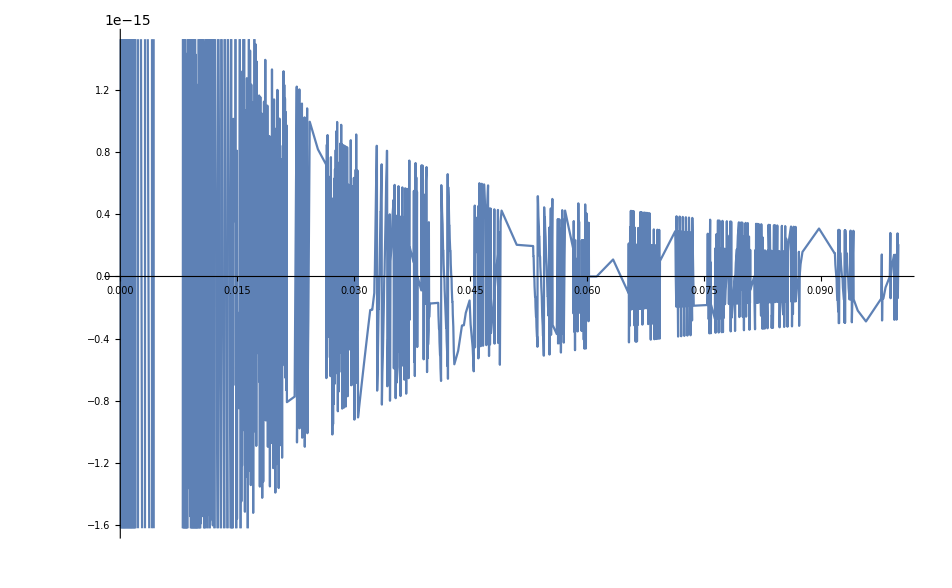

```mathematica
Plot[(-1+√((-1+a)^2)+a)/(2 a),{a,0.0000001,0.1}]
```

```mathematica
Limit[(-1+√((-1+a)^2)+a)/(2 a),a-> 0]
```

0

```mathematica
Simplify[Solve[{D[p*(1-((1+a+k-√((-1-a-k)^2-4 a p))/(2 a)))-k^2,p]== 0,D[p*(1-((1+a+k-√((-1-a-k)^2-4 a p))/(2 a)))-k^2,k]== 0,k∈Reals,p∈Reals,a∈Reals,0<a<1,p>0,k>0},{p,k}]]
```

{{p→ConditionalExpression[Root[-8 a^2-16 a^3-8 a^4+(18 a+20 a^2+68 a^3+16 a^4) #1+(-9-34 a-4 a^2-72 a^3) #1^2+16 #1^3&,2],1/12 (3+√(-51+12 √19))≤a<1],k→ConditionalExpression[Root[1+2 a+a^2-2 Root[-8 a^2-16 a^3-8 a^4+(18 a+20 a^2+68 a^3+16 a^4) #1+(-9-34 a-4 a^2-72 a^3) #1^2+16 #1^3&,2]-8 a Root[-8 a^2-16 a^3-8 a^4+(18 a+20 a^2+68 a^3+16 a^4) #1+(-9-34 a-4 a^2-72 a^3) #1^2+16 #1^3&,2]-2 a^2 Root[-8 a^2-16 a^3-8 a^4+(18 a+20 a^2+68 a^3+16 a^4) #1+(-9-34 a-4 a^2-72 a^3) #1^2+16 #1^3&,2]+9 a Root[-8 a^2-16 a^3-8 a^4+(18 a+20 a^2+68 a^3+16 a^4) #1+(-9-34 a-4 a^2-72 a^3) #1^2+16 #1^3&,2]^2+(3+4 a+a^2-4 Root[-8 a^2-16 a^3-8 a^4+(18 a+20 a^2+68 a^3+16 a^4) #1+(-9-34 a-4 a^2-72 a^3) #1^2+16 #1^3&,2]-8 a Root[-8 a^2-16 a^3-8 a^4+(18 a+20 a^2+68 a^3+16 a^4) #1+(-9-34 a-4 a^2-72 a^3) #1^2+16 #1^3&,2]) #1+(3+2 a-2 Root[-8 a^2-16 a^3-8 a^4+(18 a+20 a^2+68 a^3+16 a^4) #1+(-9-34 a-4 a^2-72 a^3) #1^2+16 #1^3&,2]) #1^2+#1^3&,3],1/12 (3+√(-51+12 √19))≤a<1]},{p→ConditionalExpression[Root[-8 a^2-16 a^3-8 a^4+(18 a+20 a^2+68 a^3+16 a^4) #1+(-9-34 a-4 a^2-72 a^3) #1^2+16 #1^3&,3],0<a<1/12 (3+√(-51+12 √19))],k→ConditionalExpression[Root[1+2 a+a^2-2 Root[-8 a^2-16 a^3-8 a^4+(18 a+20 a^2+68 a^3+16 a^4) #1+(-9-34 a-4 a^2-72 a^3) #1^2+16 #1^3&,3]-8 a Root[-8 a^2-16 a^3-8 a^4+(18 a+20 a^2+68 a^3+16 a^4) #1+(-9-34 a-4 a^2-72 a^3) #1^2+16 #1^3&,3]-2 a^2 Root[-8 a^2-16 a^3-8 a^4+(18 a+20 a^2+68 a^3+16 a^4) #1+(-9-34 a-4 a^2-72 a^3) #1^2+16 #1^3&,3]+9 a Root[-8 a^2-16 a^3-8 a^4+(18 a+20 a^2+68 a^3+16 a^4) #1+(-9-34 a-4 a^2-72 a^3) #1^2+16 #1^3&,3]^2+(3+4 a+a^2-4 Root[-8 a^2-16 a^3-8 a^4+(18 a+20 a^2+68 a^3+16 a^4) #1+(-9-34 a-4 a^2-72 a^3) #1^2+16 #1^3&,3]-8 a Root[-8 a^2-16 a^3-8 a^4+(18 a+20 a^2+68 a^3+16 a^4) #1+(-9-34 a-4 a^2-72 a^3) #1^2+16 #1^3&,3]) #1+(3+2 a-2 Root[-8 a^2-16 a^3-8 a^4+(18 a+20 a^2+68 a^3+16 a^4) #1+(-9-34 a-4 a^2-72 a^3) #1^2+16 #1^3&,3]) #1^2+#1^3&,3],0<a<1/12 (3+√(-51+12 √19))]}}

```mathematica
No norm dependence
```

```mathematica
Solve[x(1+k)-p== 0,x]
```

{{x→p/(1+k)}}

```mathematica
Solve[{D[p(1-p/(1+k))-k^2,p]==0,D[p(1-p/(1+k))-k^2,k]==0},{p,k}]
```

{{p→9/16,k→1/8}}

```mathematica
Simplify[9/16(1-(9/16)/(1+1/8))-(1/8)^2]
```

17/64